```mathematica
ClearAll["Global`*"]
```

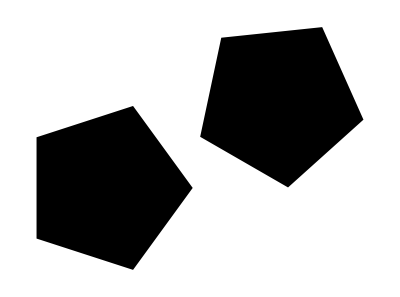

```mathematica
rtf=RotationMatrix[2Pi/5];
rtfpw[x_]:=MatrixPower[rtf,x];
vert=Table[rtfpw[i].{1,0},{i,0,4}];
c[x_,y_]:={x,y};
p[x_,y_,t_]:=(c[x,y]+#&)/@(RotationMatrix[t].#&/@vert);

Graphics[{Polygon@p[0,0,0],Polygon@p[2,1,Pi/3]}]
```